## Импорт библиотек

```mathematica
If[$FrontEnd =!= Null, AppendTo[$Path, FileNameJoin[{NotebookDirectory[], #}]]&/@{"../../lib/mathematica","../lib"}];

(Once@Get[#] &) /@ { "Formal.m", "Features.m", "Ricci_grav.m", "Parameters.m", "Cache.m","aux-2-grav-generic.m" };
```

SetDelayed::write: Tag Div in Div[V_] is Protected.

```mathematica
EnableFeature[{Formatter[DD],Formatter[Tensor]}];
```

## Определения

### Система координат

```mathematica
Spher;
RecalculateGrav[];
```

### Базовые определения

#### Константы

```mathematica
l1=l(l+1)/2;
l2=(l-1)(l+2);
l3=l1 l2 / 2;
```

```mathematica
sql2=√l2;
```

#### Тензоры

```mathematica
thmask[Odd]=<|12->0,Even->0,Odd->0,13->1,23->1|>;
thmask[Even]=<|12->1,Even->1,Odd->1,13->0,23->0|>;

thmasked[m_][th_Association]:=th thmask[m];

metr={{1/r,1,Sin[u]},{1,r ,r Sin[u]},{Sin[u],r Sin[u],r Sin[u]^2}};

tha=<|KeyValueMap[(#1->(f[#1])#2)&,<|
12->LegendreP[l,1,Cos[u]],
Even->LegendreP[l,Cos[u]],
Odd->LegendreP[l,2,Cos[u]],
13->LegendreP[l,1,Cos[u]],
23->LegendreP[l,2,Cos[u]]
|>]|>;

MakeTensor[th_Association]:=metr{{-2th[Even],th[12],th[13]},{th[12],th[Even]+th[Odd],th[23]},{th[13],th[23],th[Even]-th[Odd]}};
MakeTensor[m_][th_Association]:=MakeTensor[th//thmasked[m]];
```

#### Решения

```mathematica
sln[Generic][f[11]]=-2sln[Generic][f[Even]];
```

```mathematica
sln[Generic][f[13]]=C[1] SphericalBesselJ[l,r ω]+C[2] SphericalBesselY[l,r ω];
sln[Generic][f[23]]=-(-2 f[r]-r f'[r])/((-1+l) (2+l))/.{f->(sln[Generic][f[13]]/.r->#&)}//FullSimplify;
```

```mathematica
sln[Generic][f[Even]]=sln[Generic][f[13]]/r;
sln[Generic][f[Odd]]=-((4+l+l^2-2 r^2 ω^2) f[r]+2 r f'[r])/((-1+l) l (1+l) (2+l))/.{f->(sln[Generic][f[Even]]/.r->#&)}//FullSimplify;
sln[Generic][f[12]]=-(4 f[r]+2 r f'[r])/(l+l^2)/.{f->(sln[Generic][f[Even]]/.r->#&)}//FullSimplify;
```

```mathematica
sln[zone__][eo:Even|Odd|All]:=Evaluate@(thmasked[eo][tha])/.{x:f[__]:>sln[zone][x]};
```

#### Операторы повышения и понижения

```mathematica
up[Scalar,sgn_:+1][f_,m_]:=D[f,u]-sgn m Cot[u]f;
up[Vector,sgn_:+1][f_,m_]:=D[f,u]-sgn m Cot[u]f+sgn Csc[u]{{0,1},{1,0}}.f;
up[Tensor,sgn_:+1][f_,m_]:=D[f,u]-sgn m Cot[u]f+2sgn Csc[u]{{0,1},{1,0}}.f;
```

```mathematica
up[All,sgn_:+1][th_,m_]:=Module[{thu=th},
thu[Even]=up[Scalar,sgn][#,m]&/@th[Even];
{thu[12],thu[13]}=up[Vector,sgn][#,m]&@{th[12],th[13]};
{thu[23],thu[Odd]}=up[Tensor,sgn][#,m]&@{th[23],th[Odd]};
thu Exp[I sgn w]//Simplify
];
```

#### Инварианты и соотношения

```mathematica
eq[sdivh][th_]:=Module[{i,j,k},Table[Sum[hh[j,k]ddd[th,i,j,k],{j,3},{k,3}],{i,3}]];
```

### Решатели и отображатели

#### Обобщенные табуляторы

```mathematica
series[zone__][eo__][{n_Integer}]:=Module[{l0},Table[series[zone][eo][l0],{l0,2,n}]];
series[zone__][eo__][l0_Integer]:=Module[{m,s,sl},
Block[{l=l0},
s=sln[zone][eo]//Normal//Association;
sl={s};
Do[AppendTo[sl,s=up[All][s,m-1]],{m,1,l0}];
];
sl
];
```

```mathematica
intern[zone__][eo__][series][n_Integer,cfg_List:{energy,pointing}]:=Module[{},
Cache[cache[zone][eo][series]=series[zone][eo][{n}],
Length[#]+1<n&];
Cache[cache[zone][eo][series,Tensor]=Table[j Exp[-I ω ct]//MakeTensor[#]&,{i,cache[zone][eo][series]},{j,i}],
Length[#]+1<n&];
If[MemberQ[cfg,energy],
Cache[cache[zone][eo][series,energy]=
ParallelTable[EvaluateAt[epsne,{th[a_,b_]:>j[[a,b]]}],{i,cache[zone][eo][series,Tensor]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,pointing],
Cache[cache[zone][eo][series,pointing]=
ParallelTable[EvaluateAt[Uine,{th[a_,b_]:>j[[a,b]]}],{i,cache[zone][eo][series,Tensor]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
];
```

#### Плоттинг

```mathematica
plt[radial][f_,range_,o:OptionsPattern[]]:=Plot[f,{r}~Join~range//Evaluate,o];
```

```mathematica
denplt[energy][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},DensityPlot[Log[Abs[f0]+1],{r}~Join~range//Evaluate,{u,0,π},o]//Quiet];
```

```mathematica
denplt[pointing,i_Integer][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},DensityPlot[Log[Abs[(f0)[[i]]]+1],{r}~Join~range//Evaluate,{u,0,π},o]//Quiet];
```

```mathematica
denplt[pointing,i_List][f_,range_,o:OptionsPattern[]]:=denplt[pointing,#][f,range,o]&/@i;
```

## Волны общего вида

### Радиальные части

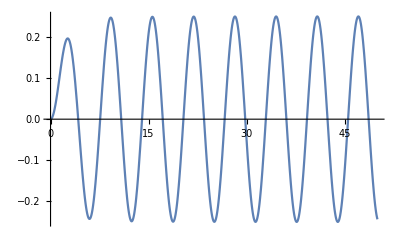
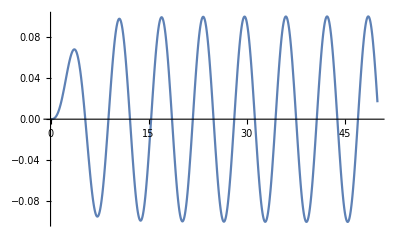
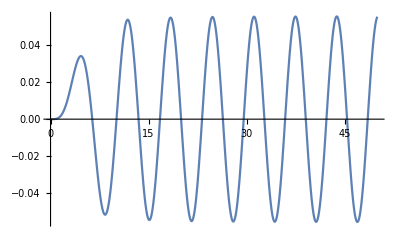
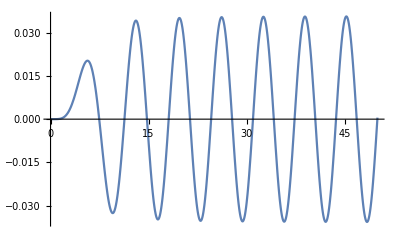
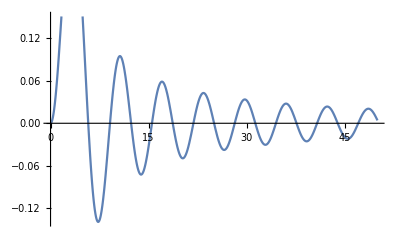
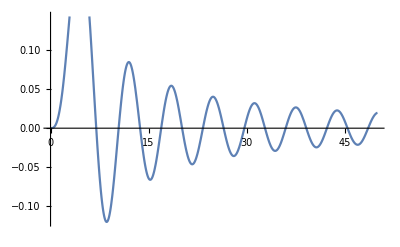
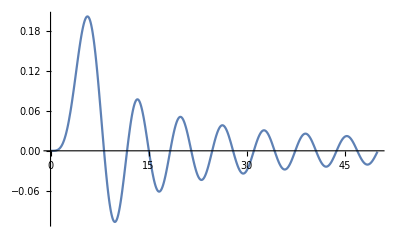
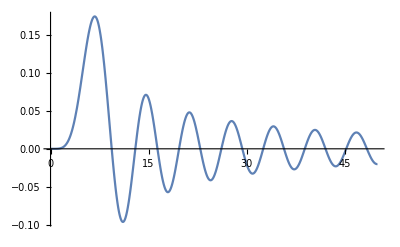
f23 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
f13 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
fe | -Graphics- | -Graphics- | -Graphics- | -Graphics-
fo | -Graphics- | -Graphics- | -Graphics- | -Graphics-
f12 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{
{"f23"}~Join~Table[plt[radial][sln[Generic][f[23]]/.{C[1]->1,C[2]->0,ω->1},{0,50}],{l,2,5}],
{"f13"}~Join~Table[plt[radial][sln[Generic][f[13]]/.{C[1]->1,C[2]->0,ω->1},{0,50}],{l,2,5}],
{"fe"}~Join~Table[plt[radial][sln[Generic][f[Even]]/.{C[3]->1,C[4]->0,ω->1},{0,50}],{l,2,5}],
{"fo"}~Join~Table[plt[radial][sln[Generic][f[Odd]]/.{C[3]->1,C[4]->0,ω->1},{0,50}],{l,2,5}],
{"f12"}~Join~Table[plt[radial][sln[Generic][f[12]]/.{C[3]->1,C[4]->0,ω->1},{0,50}],{l,2,5}]
},Frame->All]
```

### Плотность и поток энергии

```mathematica
intern[Generic][Odd][series][3];
```

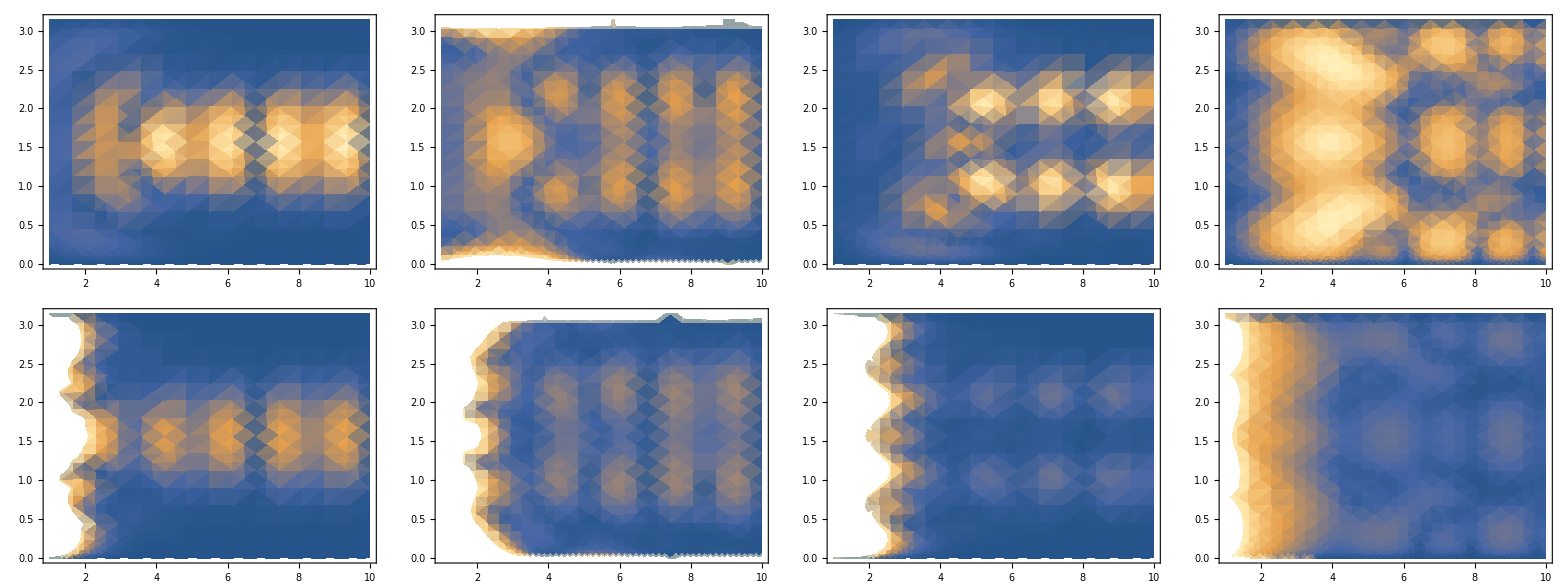

```mathematica
Table[denplt[energy][#,{1,10},MaxRecursion->1]&/@(cache[Generic][Odd][series,energy][[Sequence@@#]]/.c&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize,{c,{{C[1]->1,C[2]->0},{C[1]->0,C[2]->1}}}]//Grid
```

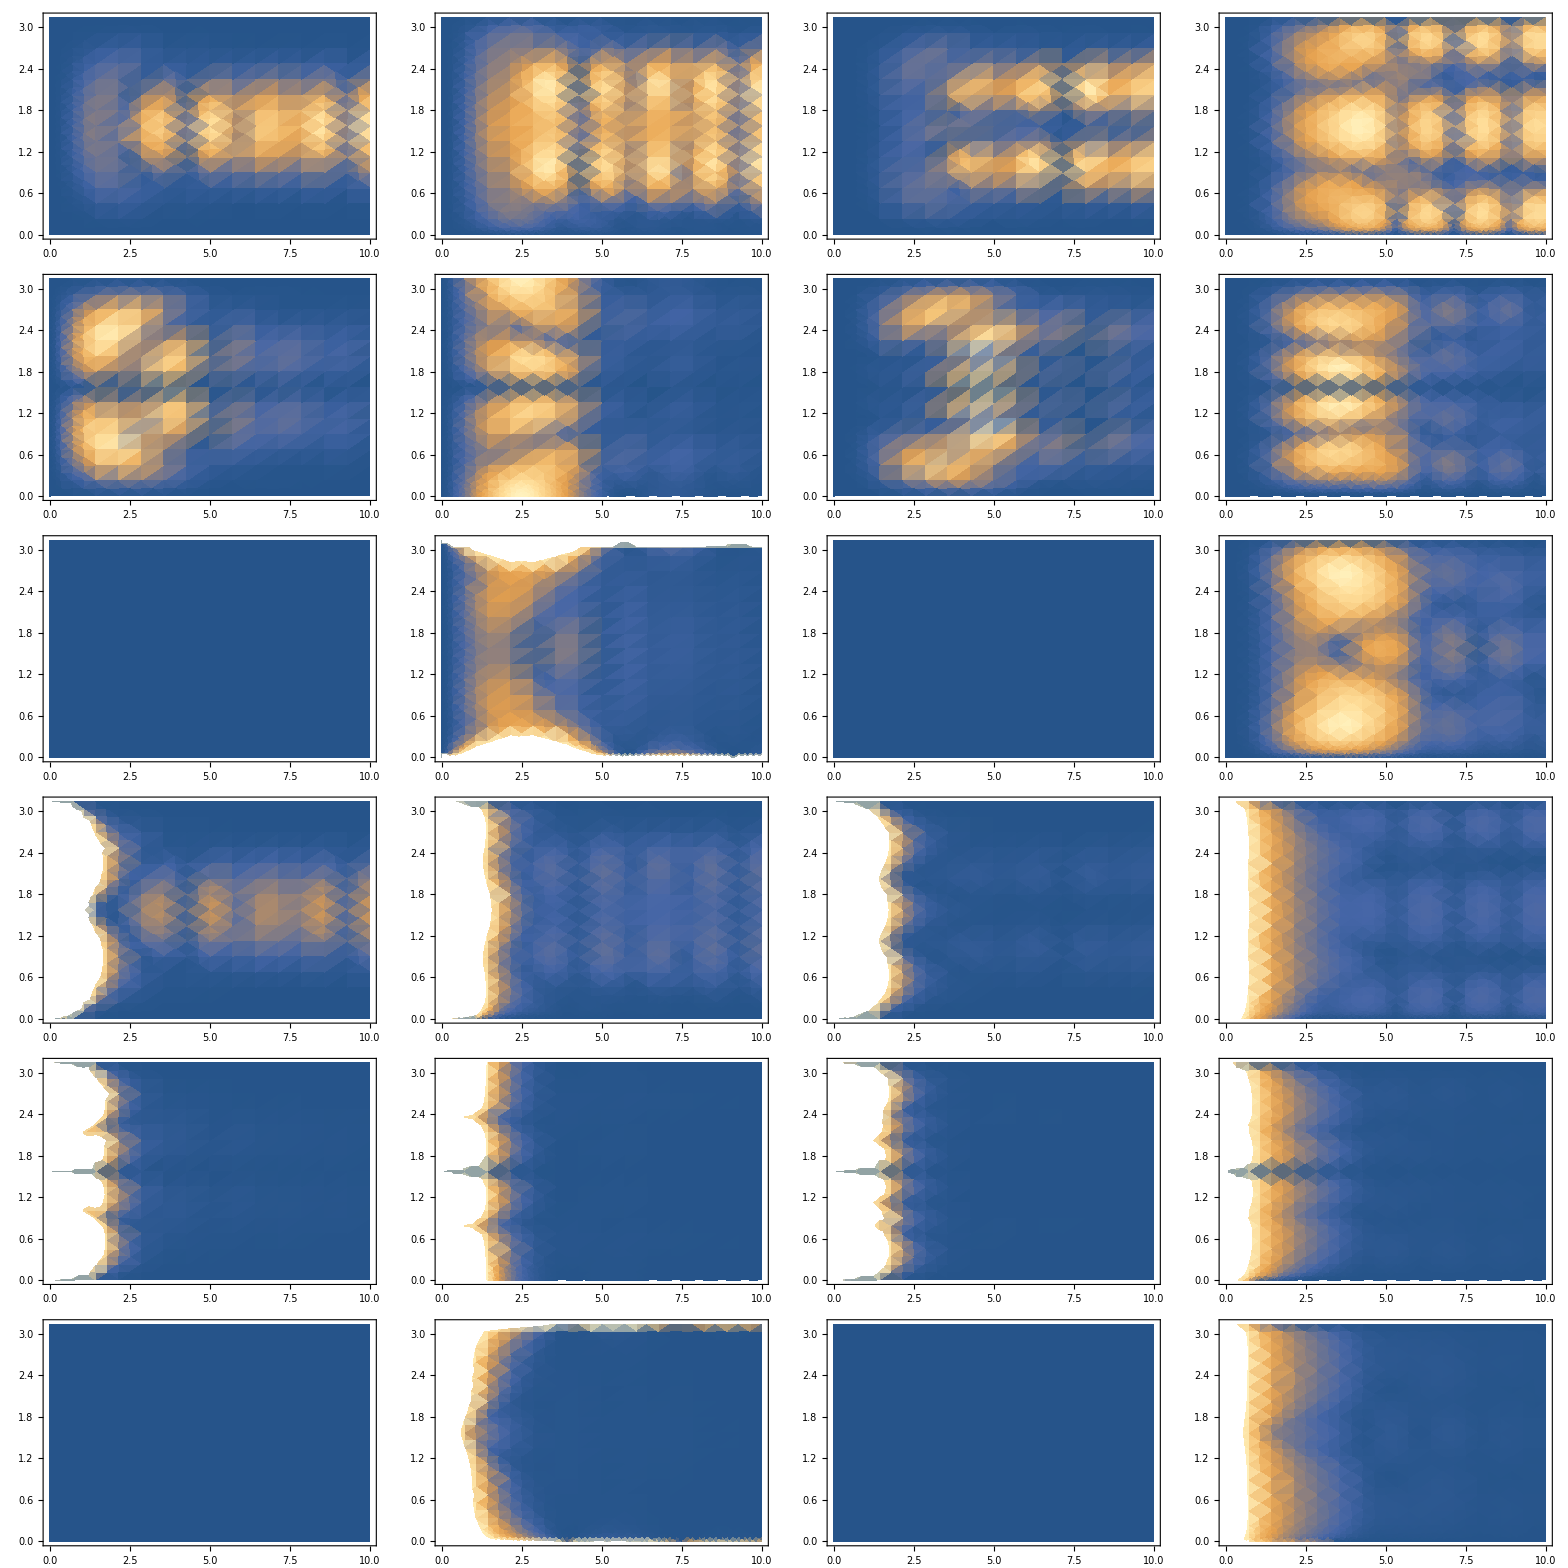

```mathematica
Table[denplt[pointing,{1,2,3}][#,{0,10},MaxRecursion->1]&/@(cache[Generic][Odd][series,pointing][[Sequence@@#]]/.c&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose,{c,{{C[1]->1,C[2]->0},{C[1]->0,C[2]->1}}}]//Flatten[#,1]&//Grid
```

```mathematica
intern[Generic][Even][series][3];
```

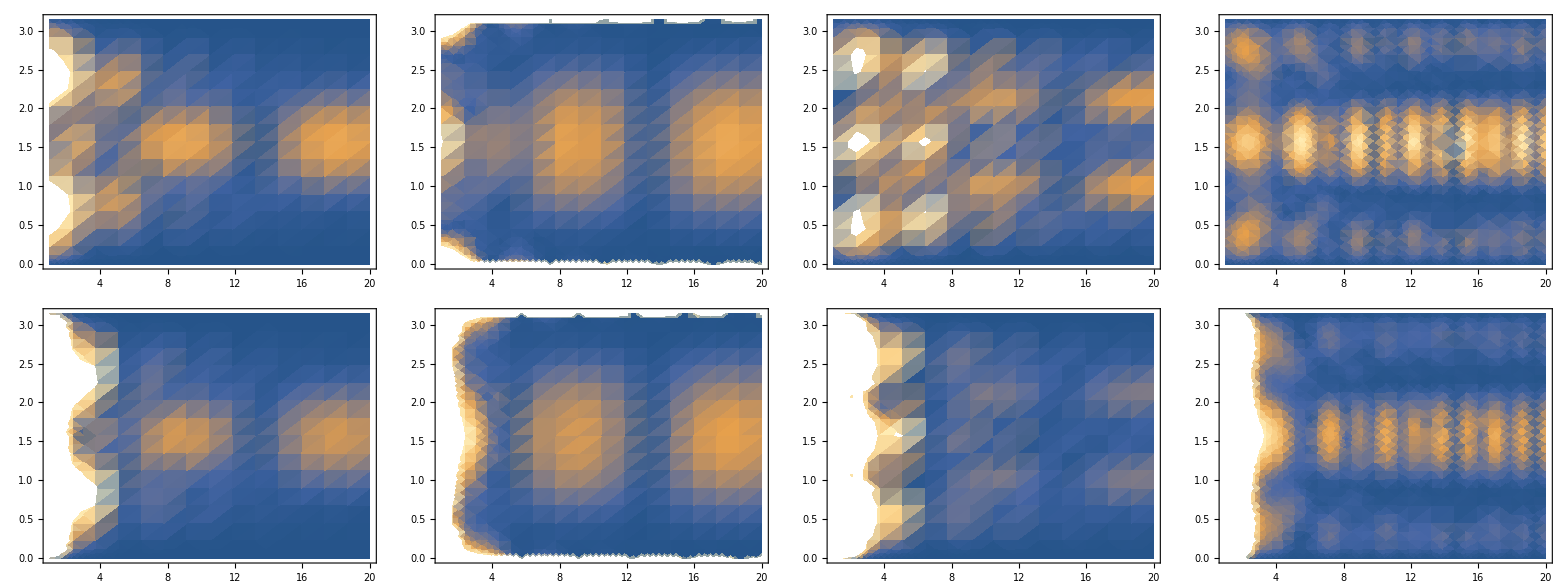

```mathematica
Table[denplt[energy][#,{1,20},MaxRecursion->2]&/@(cache[Generic][Even][series,energy][[Sequence@@#]]/.c&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize,{c,{{C[3]->1,C[4]->0},{C[3]->0,C[4]->1}}}]//Grid
```

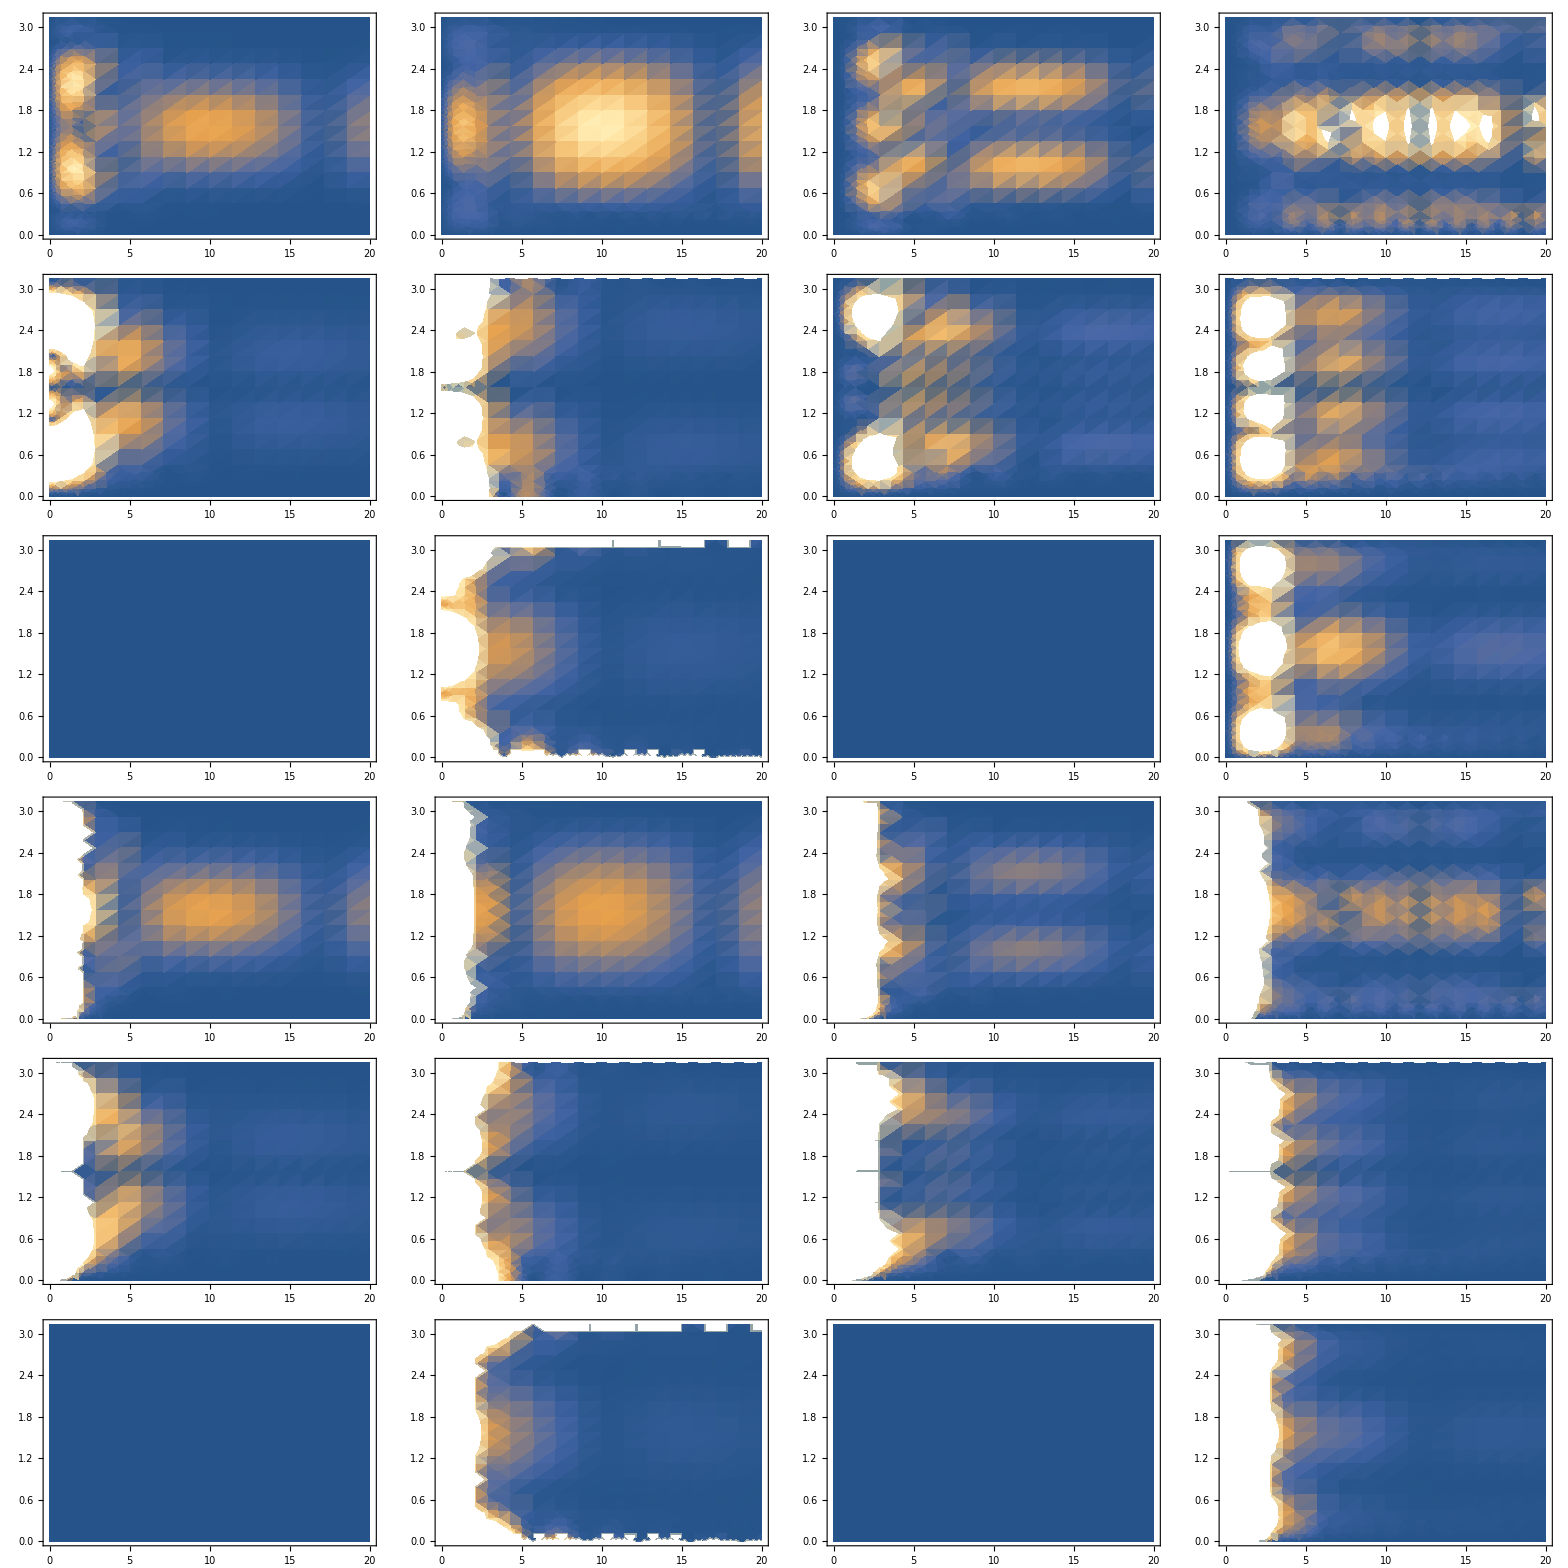

```mathematica
Table[denplt[pointing,{1,2,3}][#,{0,20},MaxRecursion->1]&/@(cache[Generic][Even][series,pointing][[Sequence@@#]]/.c&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose,{c,{{C[3]->1,C[4]->0},{C[3]->0,C[4]->1}}}]//Flatten[#,1]&//Grid
```

### Различные соотношения

```mathematica
intern[Generic][Odd][series][5,{}]
```

```mathematica
eq[sdivh][cache[Generic][Odd][series,Tensor][[Sequence@@#]]]&/@{{1,1},{2,1},{3,1},{4,1}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],ω->1,ct->0}//Simplify
```

{{{0,0,0.+4.85723×10^-17 C[1]+5.55112×10^-17 C[2]},{0,0,-8.32667×10^-17 C[1]-1.11022×10^-16 C[2]},{0,0,0.+2.77556×10^-17 C[1]},{0,0,-1.73472×10^-17 C[1]-1.11716×10^-15 C[2]}},{{0,0,0.},{0,0,-6.59195×10^-17 C[1]-5.55112×10^-17 C[2]},{0,0,5.20417×10^-17 C[1]+2.77556×10^-17 C[2]},{0,0,1.38778×10^-17 C[1]+4.16334×10^-17 C[2]}},{{0,0,0.-2.77556×10^-17 C[1]+2.77556×10^-17 C[2]},{0,0,0.-6.245×10^-17 C[1]},{0,0,0.},{0,0,0.+3.46945×10^-18 C[1]}},{{0,0,0.-2.77556×10^-17 C[1]+6.93889×10^-18 C[2]},{0,0,-8.32667×10^-17 C[1]-5.55112×10^-17 C[2]},{0,0,5.63785×10^-18 C[1]-1.38778×10^-17 C[2]},{0,0,-3.1225×10^-17 C[1]+2.77556×10^-17 C[2]}}}

```mathematica
eq[sdivh][cache[Generic][Odd][series,Tensor][[Sequence@@#]]]&/@{{1,2},{2,3}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],w->RandomReal[{0,2π}],ω->1,ct->0}//Simplify
```

{{{(0.+0. ⅈ)+(0.230768+0.59507 ⅈ) C[1]-(0.20635+0.532105 ⅈ) C[2],(0.31132-0.257833 ⅈ) C[1]+(0.192222-0.159197 ⅈ) C[2],(-0.0834834+0.00402659 ⅈ) C[1]-(0.0515461-0.00248618 ⅈ) C[2]},{(-0.0612041+1.344 ⅈ) C[1]+(0.20449-4.49047 ⅈ) C[2],(0.+0. ⅈ)-(3.91775-11.6452 ⅈ) C[1]-(1.42283-4.22927 ⅈ) C[2],(2.26761+0.872376 ⅈ) C[1]+(0.823542+0.316826 ⅈ) C[2]}},{{(0.+0. ⅈ)+(0.15554+0.401082 ⅈ) C[1]-(0.0380068+0.098006 ⅈ) C[2],(0.14986-0.124112 ⅈ) C[1]+(0.278554-0.230696 ⅈ) C[2],(-0.0401862+0.00193827 ⅈ) C[1]-(0.0746968-0.00360279 ⅈ) C[2]},{(-0.0565061+1.24084 ⅈ) C[1]+(0.0811948-1.78298 ⅈ) C[2],(0.+0. ⅈ)-(3.68232-10.9454 ⅈ) C[1]-(1.80438-5.36338 ⅈ) C[2],(2.13134+0.819952 ⅈ) C[1]+(1.04438+0.401786 ⅈ) C[2]}},{{(0.+0. ⅈ)+(0.089801+0.231565 ⅈ) C[1]+(0.0276678+0.0713455 ⅈ) C[2],(-0.0212179+0.0175725 ⅈ) C[1]+(0.274716-0.227517 ⅈ) C[2],(0.00568977-0.00027443 ⅈ) C[1]-(0.0736677-0.00355316 ⅈ) C[2]},{(-0.046569+1.02262 ⅈ) C[1]+(0.0288161-0.632782 ⅈ) C[2],(0.+0. ⅈ)-(2.58001-7.6689 ⅈ) C[1]-(2.83938-8.43983 ⅈ) C[2],(1.49332+0.574499 ⅈ) C[1]+(1.64344+0.632251 ⅈ) C[2]}},{{(0.+0. ⅈ)+(0.0387667+0.0999657 ⅈ) C[1]+(0.0458031+0.11811 ⅈ) C[2],(-0.151459+0.125437 ⅈ) C[1]+(0.189975-0.157335 ⅈ) C[2],(0.0406151-0.00195896 ⅈ) C[1]-(0.0509435-0.00245712 ⅈ) C[2]},{(-0.0337114+0.74028 ⅈ) C[1]+(0.00277576-0.0609538 ⅈ) C[2],(0.+0. ⅈ)-(0.9048-2.68945 ⅈ) C[1]-(3.39537-10.0925 ⅈ) C[2],(0.523702+0.201474 ⅈ) C[1]+(1.96525+0.756057 ⅈ) C[2]}}}

```mathematica
intern[Generic][Even][series][5,{}]
```

```mathematica
eq[sdivh][cache[Generic][Even][series,Tensor][[Sequence@@#]]]&/@{{1,1},{2,1},{3,1},{4,1}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],ω->1,ct->0}//Simplify
```

{{{0.00444967 C[3]+0.00731518 C[4],0.0371496 C[3]-0.124121 C[4],0},{0.0157927 C[3]+0.025963 C[4],0.0281933 C[3]-0.0252101 C[4],0},{-0.0108923 C[3]-0.101103 C[4],0.00417883 C[3]-0.0391334 C[4],0},{0.00211145 C[3]+0.207089 C[4],-0.00877465 C[3]+0.788387 C[4],0}},{{0.000746942 C[3]+0.00489937 C[4],0.113899 C[3]-0.0777331 C[4],0},{0.0092889 C[3]+0.0125143 C[4],0.00376504 C[3]+0.0222372 C[4],0},{-0.0094457 C[3]-0.0234489 C[4],0.00338958 C[3]-0.00794696 C[4],0},{0.00243403 C[3]+0.0379937 C[4],-0.0108886 C[3]+0.173056 C[4],0}},{{-0.00106215 C[3]+0.00292788 C[4],0.132152 C[3]+0.00298869 C[4],0},{0.00386444 C[3]+0.00921362 C[4],-0.0193797 C[3]+0.0266351 C[4],0},{-0.00701601 C[3]-0.0097332 C[4],0.0015259 C[3]+0.000467006 C[4],0},{0.00244297 C[3]+0.00962519 C[4],-0.0104974 C[3]+0.0449404 C[4],0}},{{-0.00162489 C[3]+0.00129323 C[4],0.0985232 C[3]+0.0734766 C[4],0},{-0.0000306045 C[3]+0.00683355 C[4],-0.0337803 C[3]+0.0127179 C[4],0},{-0.00416168 C[3]-0.00684414 C[4],-0.000873067 C[3]+0.00281767 C[4],0},{0.00212939 C[3]+0.00360808 C[4],-0.00700794 C[3]+0.00747412 C[4],0}}}

```mathematica
eq[sdivh][cache[Generic][Even][series,Tensor][[Sequence@@#]]]&/@{{1,2},{2,3}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],w->RandomReal[{0,2π}],ω->1,ct->0}//Simplify
```

{{{(0.0313866-0.128859 ⅈ) C[3]+(0.0515991-0.211842 ⅈ) C[4],(-0.0654102+0.0393782 ⅈ) C[3]+(0.16543+0.0721383 ⅈ) C[4],(-0.0201144-0.0311284 ⅈ) C[3]+(0.0285557+0.0375884 ⅈ) C[4]},{(-0.311674+0.06303 ⅈ) C[3]-(0.512388-0.10362 ⅈ) C[4],(0.132129-0.137608 ⅈ) C[3]+(1.99445+1.09356 ⅈ) C[4],(-0.0153371+0.0113384 ⅈ) C[3]-(0.134399-0.422358 ⅈ) C[4]}},{{(0.0052687-0.0216308 ⅈ) C[3]+(0.0345586-0.141882 ⅈ) C[4],(-0.148625-0.0783969 ⅈ) C[3]+(0.095023+0.0780868 ⅈ) C[4],(-0.0238894-0.0305154 ⅈ) C[3]+(0.0116397+0.0128109 ⅈ) C[4]},{(-0.183319+0.0370727 ⅈ) C[3]-(0.246974-0.0499455 ⅈ) C[4],(-0.664152-0.331589 ⅈ) C[3]+(1.93055+0.730466 ⅈ) C[4],(0.0457523-0.138065 ⅈ) C[3]-(0.14014-0.382836 ⅈ) C[4]}},{{(-0.00749211+0.0307591 ⅈ) C[3]+(0.0206524-0.0847892 ⅈ) C[4],(-0.163915-0.123667 ⅈ) C[3]-(0.00611844-0.00645169 ⅈ) C[4],(-0.0215123-0.0247419 ⅈ) C[3]-(0.00224122+0.00357489 ⅈ) C[4]},{(-0.0762659+0.0154233 ⅈ) C[3]-(0.181834-0.0367723 ⅈ) C[4],(-1.34121-0.479826 ⅈ) C[3]+(1.34697+0.431438 ⅈ) C[4],(0.0982063-0.263776 ⅈ) C[3]-(0.100173-0.260912 ⅈ) C[4]}},{{(-0.0114615+0.0470555 ⅈ) C[3]+(0.00912207-0.037451 ⅈ) C[4],(-0.119553-0.102364 ⅈ) C[3]-(0.0907487+0.0702475 ⅈ) C[4],(-0.0141091-0.0151311 ⅈ) C[3]-(0.0116784+0.0132712 ⅈ) C[4]},{(0.000603989-0.000122145 ⅈ) C[3]-(0.134862-0.0272732 ⅈ) C[4],(-1.66832-0.528805 ⅈ) C[3]+(0.488219+0.134828 ⅈ) C[4],(0.124242-0.322718 ⅈ) C[3]-(0.0369685-0.0928623 ⅈ) C[4]}}}